```mathematica
(* This notebook analyzes the dynamics of NNC and BBC estimates of the FPR and FNR (mostly the latter) of the PR monitor depending on the window size (d). *)
```

```mathematica
(** FPR ESTIMATES 
too small for the evaluation**)
```

```mathematica
(* BBC by D from directories, calculated by scripts *) 
getMonValues[dataDirPathForSeshNum[All], "FPR"]
```

{0.010586,0.001484,0.000467,0.000388,0.000271,0.000193,0.000115,0.000115,0.000114,0.000114,0.000038,0.000038,0.000038,0.000038,0.000037,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

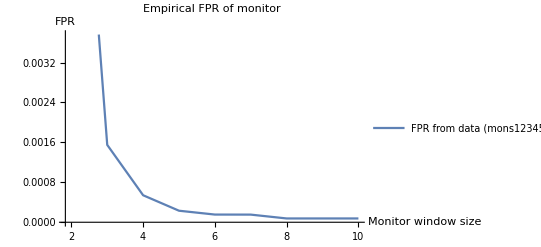

```mathematica
(* BBC for PR monitor FPR by window size, from mons12345 (13755 frames)  *)
empFPRbyWinSizeMons12345 = ListLinePlot[{{2, 0.010964} ,{3, 0.001550}, {4,0.000541},{5,0.000231},{6,0.000154},{7,0.000153},{8,0.000076},{9,0.000076},{10,0.000076}}, PlotLabel->"Empirical FPR of monitor", AxesLabel->{"Monitor window size", "FPR"},  PlotLegends->{"FPR from data (mons12345, 13.7k frames)"}]
```

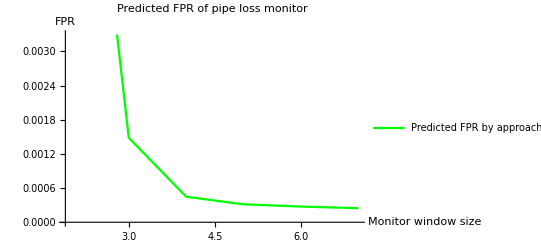

```mathematica
(* NCC FPR estimates based on iter12345&det12345, priors/conditionals are from priorcond_iter12345_win6_stats.txt*) predFPRbyModSize = ListLinePlot[{{1, 0.010340023070913059} ,{2, 0.001483774261742787}, {3,0.00044828540282684716},{4,0.00031501632612945194},{5,0},{6,0},{7,0},{8,0},{9,0}, {10,0}}, PlotLabel->"Predicted FPR of monitor (FPR", AxesLabel->{"Modality window size", "FPR"},  PlotStyle->Green, PlotLegends->{"Predicted FPR by approach"}];
predFPRbyWinSize = ListLinePlot[{{2, 0.010340023070913059} ,{3, 0.001483774261742787}, {4,0.00044828540282684716},{5,0.00031501632612945194},{6,0.00027563453619774763},{7,0.00024669065927919963}(*,{8,0},{9,0},{10,0}*)}, PlotLabel->"Predicted FPR of pipe loss monitor", AxesLabel->{"Monitor window size", "FPR"},  PlotStyle->Green, PlotLegends->{"Predicted FPR by approach"}]
```

```mathematica
(** FNR ESTIMATES **)
```

```mathematica
(* NCC formula - monitor FNR with modality size *) 
betaERS := 1 - (1-alphaPI)(1 - alphaPI - pNChoPI)^d ;
predFNRbyModSize = ListLinePlot[Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , d == #}, {#, Simplify@betaERS}]& /@ Table[n, {n,1, 9, 1}], (* this is mon win - 1 *)
PlotLabel -> "Monitor FNR by monitor size - 1", AxesLabel -> {"Modality size (= monwin size - 1)", "Monitor FNR"},PlotStyle->Magenta];

(* NCC formula - monitor FNR with monitor window size *) 
betaERSmonwin := 1 - (1-alphaPI)(1 - alphaPI - pNChoPI)^(monwin-1);
```

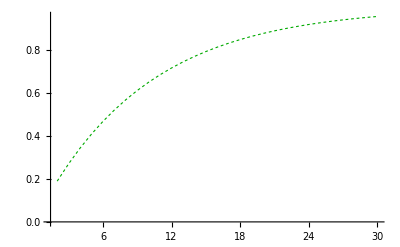

```mathematica
(* ECC chart *) 
gtFNRChart =ListLinePlot[Assuming[{alphaPI==0.1  , pNChoPI==0 , monwin== #}, {#, Simplify@betaERSmonwin}]& /@ Table[n, {n,2,30, 1}], (* this is mon win - 1 *)
PlotStyle->{Dashing[0.005],Darker@Green, Thickness[0.002]}, (*PlotLegends->{"Ground-truth FNR"},*) PlotRange->All]
```

```mathematica
(* BBC numbers *) 
estFNRChartSesh4567 = ListLinePlot[Inner[List, Range[2,30], getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR"], List], PlotStyle->{ColorData[97,"ColorList"][[2]], Thickness[0.002](*Darker@Blue,Dotted*)}(*, PlotLegends->{"Data estimate (7.7 hrs)"}*)]

(* NCC numbers *)
```

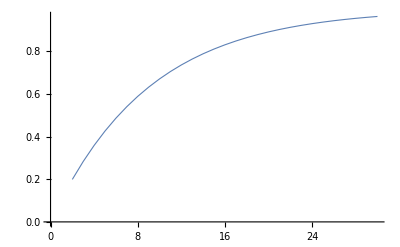

```mathematica
predFNRchartSesh4567 = ListLinePlot[Inner[List, Range[2,30], predPrMonFNRTheor[predFPRfromData[fullStatelessTripleListNoRedun@{4,5,6,7}, detFilenames],#]&/@ Range[2,30], List], PlotStyle->{ColorData[97,"ColorList"][[1]], Thickness[0.002]}]
```

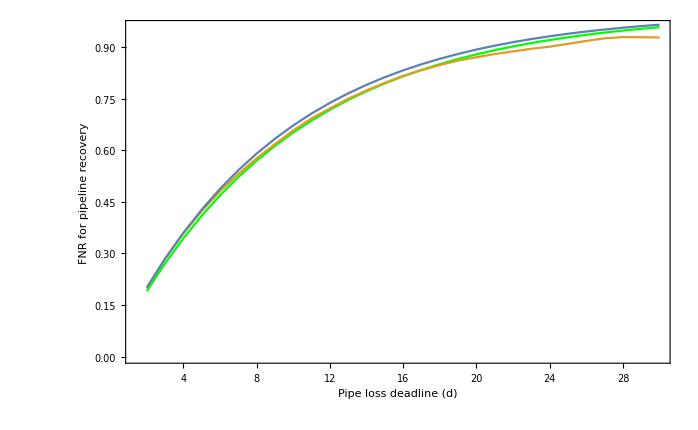

```mathematica
(*** PLOT COMBINATIONS ***) 
Show[gtFNRChart,estFNRChartSesh4567, predFNRchartSesh4567,(* AxesLabel -> {"Monitor window size", "Monitor FNR"}*)Frame->True, FrameLabel->{StringJoin["Pipe loss deadline ", ToString[ Style["(d)", Italic], StandardForm] ],"FNR for pipeline recovery"}, ImageSize->1500, BaseStyle-> {FontSize->15}]
```

```mathematica
(* PRODUCTION-READY PLOT *)
```

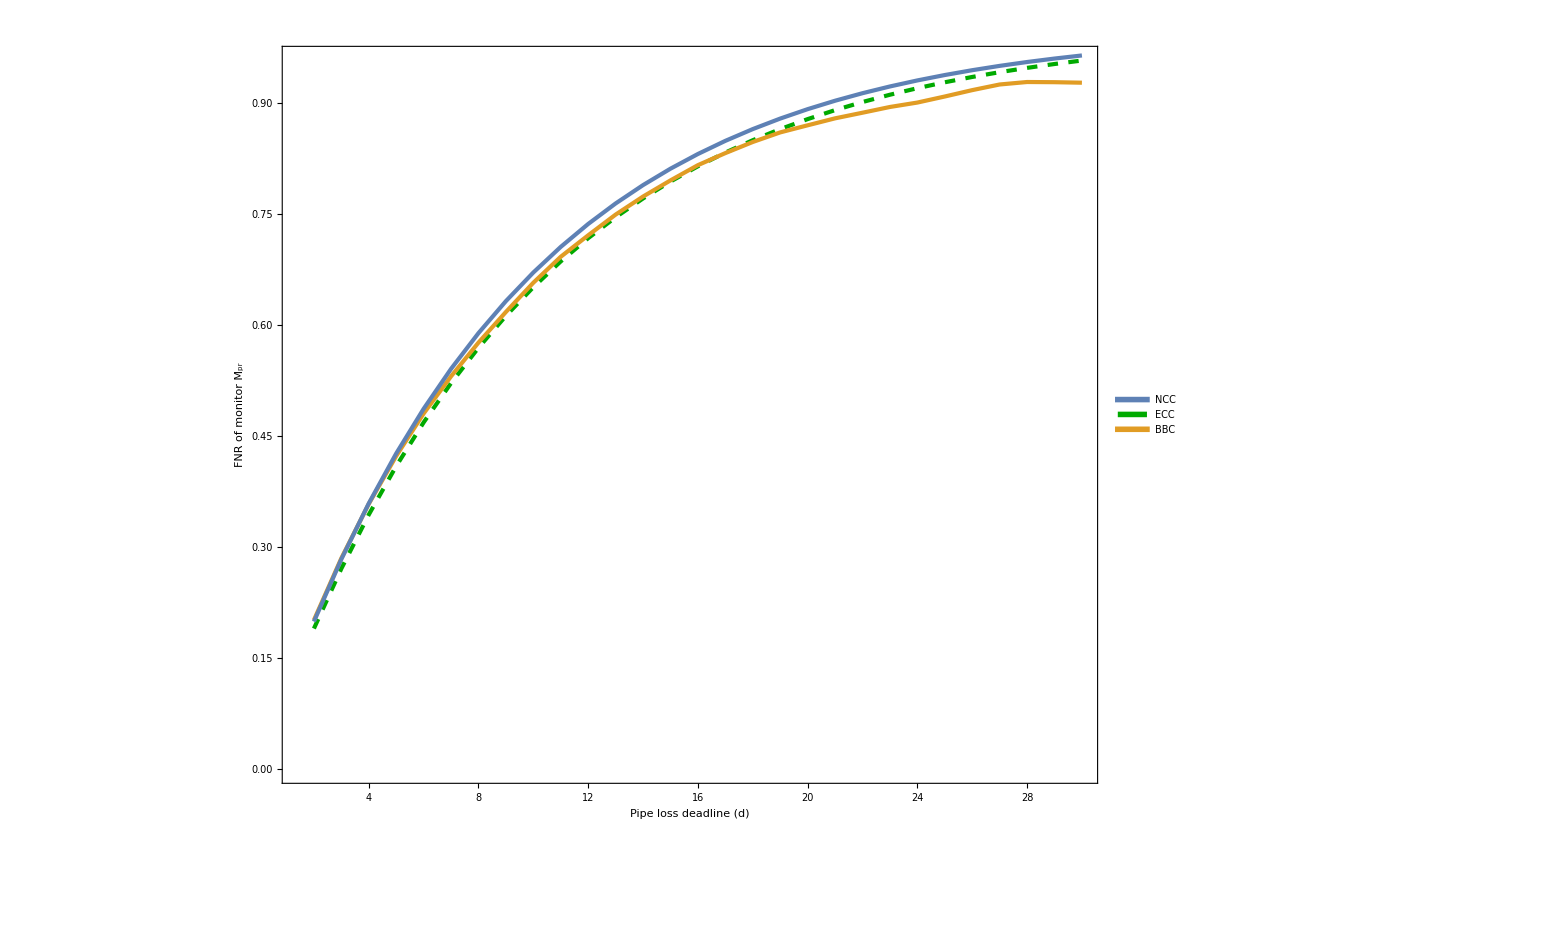

```mathematica
Legended[Show[gtFNRChart,estFNRChartSesh4567, predFNRchartSesh4567,(*  AxesLabel -> {"Monitor window size", "Monitor FNR"}*)Frame->True, FrameLabel->{StringJoin["Pipe loss deadline ", ToString[ Style["(d)", Italic], StandardForm] ],StringJoin["FNR of monitor ", ToString[Style[Subscript[ "M", "pr"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}], 
Placed[LineLegend[Directive@@@{{ColorData[97,"ColorList"][[1]],AbsoluteThickness[5]},{AbsoluteDashing[10],AbsoluteThickness[5],Darker@Green} , {ColorData[97,"ColorList"][[2]],AbsoluteThickness[5]}},{"NCC","ECC", "BBC"}
(*, LegendMarkers->Graphics[{ Thickness[0.3],Line[{{-10,0},{10,0}}]}]*)(*LegendMarkers->Automatic*)],{0.1,0.85}]]
```

```mathematica
(** RMSE ESTIMATES ON FULL DATASET **)
```

```mathematica
bbcPrEsts = getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR"]
```

{0.201409,0.284999,0.358476,0.423147,0.480576,0.53085,0.576453,0.61784,0.65734,0.692441,0.721449,0.749419,0.77381,0.795633,0.816231,0.8325,0.847522,0.860479,0.870064,0.879467,0.887072,0.894829,0.900802,0.908985,0.917598,0.925217,0.928571,0.928328,0.927632}

```mathematica
nccPrEsts = N@predPrMonFNRTheor[predFPRfromData[fullStatelessTripleListNoRedun@{4,5,6,7}, detFilenames],#]&/@ Range[2,30]
```

{0.199446,0.283715,0.359113,0.426575,0.486936,0.540942,0.589264,0.6325,0.671184,0.705796,0.736765,0.764474,0.789266,0.811449,0.831296,0.849054,0.864943,0.87916,0.89188,0.903261,0.913444,0.922555,0.930707,0.938001,0.944527,0.950367,0.955591,0.960266,0.964448}

```mathematica
eccPrEsts = Assuming[{alphaPI==0.1 (* cheating a bit *) , pNChoPI==0 , monwin== #}, Simplify@betaERSmonwin]& /@ Table[n, {n,2,30, 1}]
```

{0.19,0.271,0.3439,0.40951,0.468559,0.521703,0.569533,0.61258,0.651322,0.686189,0.71757,0.745813,0.771232,0.794109,0.814698,0.833228,0.849905,0.864915,0.878423,0.890581,0.901523,0.911371,0.920234,0.92821,0.935389,0.94185,0.947665,0.952899,0.957609}

```mathematica
(* final BBC RMSE value *)
bbcRmse = Sqrt@Mean[(eccPrEsts - bbcPrEsts)^2 ]
```

0.0131986

```mathematica
(* final NCC RMSE value *)
nccRmse = Sqrt@Mean[(eccPrEsts - nccPrEsts)^2 ]
```

0.0149465